```mathematica
data = {{1/10,529/436},{1/9,436/352},{1/8,352/277},{1/7,277/211},{1/6,211/154},{1/5,154/106},{1/4,106/67},{1/3,67/37},{1/2,37/16},{1,16/4}}
datam = {{1/10,529/436},{1/9,436/352},{1/8,352/277},{1/7,277/211},{1/6,211/154},{1/5,154/106},{1/4,106/67}}
```

{{1/10,529/436},{1/9,109/88},{1/8,352/277},{1/7,277/211},{1/6,211/154},{1/5,77/53},{1/4,106/67},{1/3,67/37},{1/2,37/16},{1,4}}

{{1/10,529/436},{1/9,109/88},{1/8,352/277},{1/7,277/211},{1/6,211/154},{1/5,77/53},{1/4,106/67}}

```mathematica
line = Fit[data,{1,x},x]
```

0.852466+3.08614 x

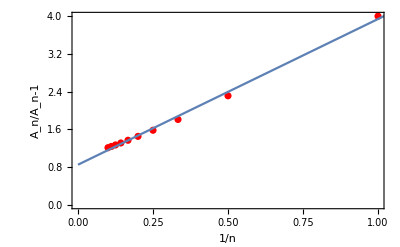

```mathematica
s = Show[ListPlot[data,PlotStyle->Red],Plot[{line},{x,0,5}],AxesStyle->Black,FrameLabel->{"1/n","A_n/A_n-1"},Frame->True]
```